# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Kagiwada-Kalaba (Ellipsoidal) Scattering

```mathematica
pEllipsoidal[u_,b_]:=b(2 Pi Log[(1+b)/(1-b)](1-b u))^-1
```

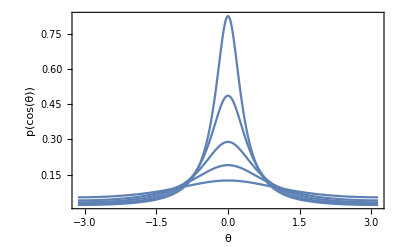

```mathematica
pEllplot=Show[
Plot[pEllipsoidal[Cos[t],.9],{t,-Pi,Pi},PlotRange->All],
Plot[pEllipsoidal[Cos[t],.8],{t,-Pi,Pi},PlotRange->All],
Plot[pEllipsoidal[Cos[t],.65],{t,-Pi,Pi},PlotRange->All],
Plot[pEllipsoidal[Cos[t],.4],{t,-Pi,Pi},PlotRange->All],
Plot[pEllipsoidal[Cos[t],.95],{t,-Pi,Pi},PlotRange->All],
Frame->True,
ImageSize->400,
FrameLabel->{{p[Cos[θ]],},{θ,"Ellipsoidal Scattering, b = 0.4, 0.65, 0.8, 0.9, 0.95"}}]
```

### sampling

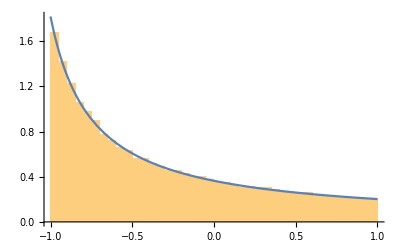

```mathematica
b=-0.8;
Show[Histogram[Map[(1-(1+b) ((1+b)/(1-b))^-#)/b&,Table[RandomReal[],{i,1,100000}]],50,"PDF"],
Plot[2 Pi pEllipsoidal[u,b],{u,-1,1}]

]
Clear[b];
```

When cosine u has been sampled with random variable ξ, what is the PDF at the sampled direction in terms of ξ?

```mathematica
FullSimplify[pEllipsoidal[(1-(1+b) ((1+b)/(1-b))^-#)/b&[ξ],b],Assumptions->0<b<1&&0<ξ<1]
```

((1-b)^-ξ b (1+b)^(-1+ξ))/(2 π Log[(1+b)/(1-b)])

### Expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pEllipsoidal[u,b]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->0<b<1]/.Log[(1+b)/(1-b)]->2 ArcTanh[b]
```

1

```mathematica
Integrate[2Pi(2k+1)pEllipsoidal[u,b]LegendreP[k,u]/.k->1,{u,-1,1},Assumptions->0<b<1]/.Log[(1+b)/(1-b)]->2 ArcTanh[b]//FullSimplify
```

3/b-3/ArcTanh[b]

```mathematica
Integrate[2Pi(2k+1)pEllipsoidal[u,b]LegendreP[k,u]/.k->2,{u,-1,1},Assumptions->0<b<1]/.Log[(1+b)/(1-b)]->2 ArcTanh[b]//FullSimplify
```

5/2 (-1+3/b^2-3/(b ArcTanh[b]))

```mathematica
Integrate[2Pi(2k+1)pEllipsoidal[u,b]LegendreP[k,u]/.k->3,{u,-1,1},Assumptions->0<b<1]/.Log[(1+b)/(1-b)]->2 ArcTanh[b]//FullSimplify
```

(7 (b (-15+4 b^2)+(15-9 b^2) ArcTanh[b]))/(6 b^3 ArcTanh[b])

```mathematica
Integrate[2Pi(2k+1)pEllipsoidal[u,b]LegendreP[k,u]/.k->4,{u,-1,1},Assumptions->0<b<1]/.Log[(1+b)/(1-b)]->2 ArcTanh[b]//FullSimplify
```

(15 b (-21+11 b^2)+9 (35-30 b^2+3 b^4) ArcTanh[b])/(8 b^4 ArcTanh[b])